The biochemical resolving power of fluorescence lifetime imaging 

Andrew L. Trinh^(1,*) and Alessandro Esposito^1
^1 MRC Cancer Unit, University of Cambridge, Cambridge, United Kingdom
*at862@cam.ac.uk

Keywords: fluorescence lifetime, resolution, microscopy, biochemistry

Published in bioRxiv: doi_________

```mathematica
(* INITIALIZATION *)
(* Define subcripted symbols *)
<<Notation`
Symbolize[Subscript[σ, _]]
(* Beep at every evaluation *)
$Post=(Beep[];#)&;
```

```mathematica
(* Define positivity of all variables, and set substitution rules *)
opts={B>0,m>1,i>1,τ>0,A>0,T>0,C>0,t≥0,p>0,Subscript[σ, irf]>0,ρ>0,ω>0,μ>0,η>0};
subs={τ->Subscript[σ, irf]/(√2 ρ),T->(ω √2 Subscript[σ, irf])/m,A->2 B/τ ,μ->η √2 Subscript[σ, irf]};
subsinv={ρ->Subscript[σ, irf]/(√2 τ),ω->(m T)/(√2 Subscript[σ, irf]),B->(A τ)/2,η->μ/(√2 Subscript[σ, irf])};
```

```mathematica
(* Exponential decay with Gaussian IRF *)
f1=FullSimplify[Convolve[PDF[NormalDistribution[μ,Subscript[σ, irf]],x],UnitStep[x] A Exp[-x/τ],x,y,Assumptions->opts],Assumptions->opts]
```

1/2 A ⅇ^((σ_irf^2-2 y τ+2 μ τ)/(2 τ^2)) Erfc[(σ_irf^2+(-y+μ) τ)/(√2 σ_irf τ)]

```mathematica
(* Expected counts within interval t, starting from time 0 *)
Λ[t_]=Simplify[Integrate[f1,{y,0,t},Assumptions->opts]//.subs,Assumptions->opts]
```

B (Erf[η]-Erf[η-t/(√2 σ_irf)]+ⅇ^(ρ (2 η+ρ)) Erfc[η+ρ]-ⅇ^(ρ (2 η+ρ-(√2 t)/σ_irf)) Erfc[η+ρ-t/(√2 σ_irf)])

```mathematica
(* Log-likelihood. Terms that do not depend on B or ρ are neglected *)

(* The derivative of the logarithm generate a denumerator that causes nbumerical instabilities. REGCNST avoids indeterminate cases of the type 1/0*)
REGCNST= 1*^-6;

LogL[B_,ρ_]=Simplify[(∑_(i=1)^m Log[REGCNST+Λ[i T]-Λ[(i-1)T]]G[i]-∑_(i=1)^m (Λ[i T]-Λ[(i-1)T]))//.T->(ω √2 Subscript[σ, irf])/m//.η->0,Assumptions->opts]
```

-B (Erf[ω]+ⅇ^(ρ^2) Erfc[ρ]-ⅇ^(ρ (ρ-2 ω)) Erfc[ρ-ω])+∑_(i=1)^m G[i] Log[1/1000000-B (Erf[((-1+i) ω)/m]+ⅇ^(ρ^2) Erfc[ρ]-ⅇ^(ρ (ρ-(2 (-1+i) ω)/m)) Erfc[ρ-((-1+i) ω)/m])+B (Erf[(i ω)/m]+ⅇ^(ρ^2) Erfc[ρ]-ⅇ^(ρ (ρ-(2 i ω)/m)) Erfc[ρ-(i ω)/m])]

```mathematica
(* Defines the counts per bin, keeping this implicit to avoid being differentiated. EG will be replaced to G[i] when computing expectations *)

EGi=FullSimplify[(Λ[i T]-Λ[(i-1) T])//.subs//.η->0,Assumptions->opts]

(* η->0 is the particular case where the is no offset on the temporal axis *)
```

-B (-1+Erf[((-1+i) ω)/m]+Erfc[(i ω)/m]+ⅇ^(ρ (ρ-(2 i ω)/m)) (Erfc[ρ-(i ω)/m]-ⅇ^((2 ρ ω)/m) Erfc[ρ+(ω-i ω)/m]))

```mathematica
(* Evaluate derivatives, elements of the Fisher information matrix *)

a=-D[LogL[B,ρ],{ρ,2}];
b=-D[LogL[B,ρ],{B,2}];
c=-D[LogL[B,ρ],{B,1},{ρ,1}];
```

```mathematica
(*F is F2->C Subscript[σ, τ]^2/τ^2;*)

(* Error propagation *)
(* Subscript[σ, τ]^2=((D[τ/.subs[[1]],{ρ,1}])^2/.subsinv)Subscript[σ, ρ]^2->(2 τ^4)/Subscript[σ, irf]^2 Subscript[σ, ρ]^2;*)
(* Fisher Information matrix inversion, firt element*)
(* Subscript[σ, ρ]=√(b/(a b - c^2)/.G[i]->EGi/.η->0)//.subsinv; *)

(* Expectations will be implicetly determined using Gi instead of G[i] and substituting B for  *)

EB=Solve[C==Λ[m T]//.subs/.η->0,B][[1]][[1]]

(* Therefore, evaluating expectations by substitution with EG and EB *)
F2ev=C(2 τ^2)/Subscript[σ, irf]^2 b/(a b - c^2)/.{G[i]->EGi}/.EB/.{ρ->Subscript[σ, irf]/(√2 τ),ω->PER/(√2 Subscript[σ, irf])};
```

B→C/(Erf[ω]+ⅇ^(ρ^2) Erfc[ρ]-ⅇ^(ρ (ρ-2 ω)) Erfc[ρ-ω])

```mathematica
(* Test *)
(* Approx solutions show that F2ev does not depend on C. This line is used only for checking  that F2ev is well behaved numerically and confirming the independency from C *)

F2ev/.{Subscript[σ, irf]->.1,τ->.01,PER->25,m->128,C->10}
```

General::munfl: Exp[-2450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

400.138

```mathematica
(* Control curves (Kollner&Wolfrum *)
F2Dirac=ExpandAll[((-1+ⅇ^(T/τ))^2 (-1+ⅇ^((m T)/τ))^2 τ^2)/((ⅇ^(T/τ)+ⅇ^((T+2 m T)/τ)-ⅇ^((m T)/τ) m^2-ⅇ^(((2+m) T)/τ) m^2+2 ⅇ^(((1+m) T)/τ) (-1+m^2)) T^2)];
```

```mathematica
τn=151;
mn=12;
σn=7;

memo=Table[100000,τn,mn,σn];
memo2=Table[100000,τn,mn,σn];



σ0={0.001,0.1,0.25,0.5,1,2,5};
τ0=Table[0.01*1.05^(i-1),{i,τn}];
m0=Table[2^i,{i,mn}];

For[τi=1,τi≤τn,τi++,
For[mi=1,mi≤mn, mi++,
For[σi=1,σi≤σn, σi++,
vals={C->1,Subscript[σ, irf]->σ0[[σi]],τ->τ0[[τi]],PER->25,m->m0[[mi]]};
tmp=(F2ev/.vals);
memo2[[τi, mi,σi]]=F2Dirac/.{T->PER/m}//.vals;
If[tmp>0.001, memo[[τi, mi,σi]]=tmp]
]
]
Print[τi]
]
Beep[]
```

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2500.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

```mathematica
Export["GaussianForMatlab.mat",memo]
```

GaussianForMatlab.mat

```mathematica
Export["GaussianForMathematica.dat",All]
```

```mathematica
memo[[1,1,1]]
```

4072.91

```mathematica
ListPlot[Table[{τ0[[τi]],memo[[τi,mi,1]]},{mi,1,mn},{τi,1,τn}],Joined->True,PlotStyle->Directive[Black,Thin,SolidData],PlotRange->{0,1}]
```

-Graphics-

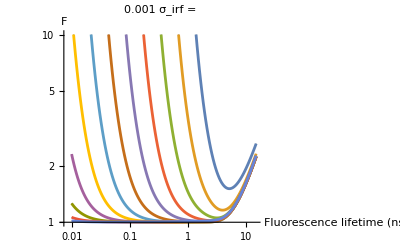

{12.5,6.25,3.125,1.5625,0.78125,0.390625,0.195313,0.0976563,0.0488281,0.0244141,0.012207,0.00610352}

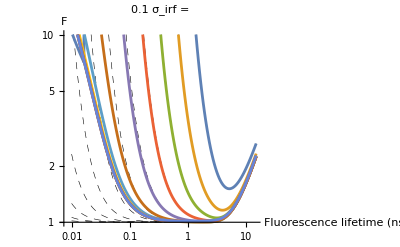

{12.5,6.25,3.125,1.5625,0.78125,0.390625,0.195313,0.0976563,0.0488281,0.0244141,0.012207,0.00610352}

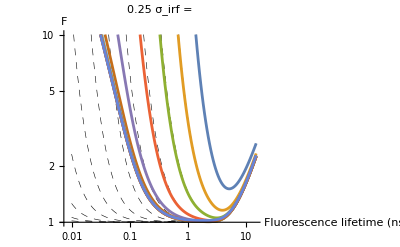

{12.5,6.25,3.125,1.5625,0.78125,0.390625,0.195313,0.0976563,0.0488281,0.0244141,0.012207,0.00610352}

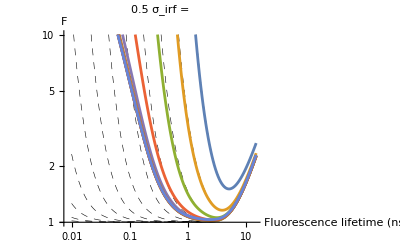

{12.5,6.25,3.125,1.5625,0.78125,0.390625,0.195313,0.0976563,0.0488281,0.0244141,0.012207,0.00610352}

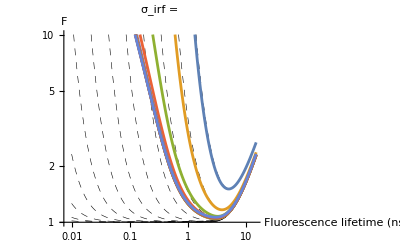

{12.5,6.25,3.125,1.5625,0.78125,0.390625,0.195313,0.0976563,0.0488281,0.0244141,0.012207,0.00610352}

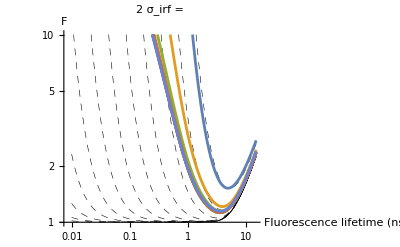

{12.5,6.25,3.125,1.5625,0.78125,0.390625,0.195313,0.0976563,0.0488281,0.0244141,0.012207,0.00610352}

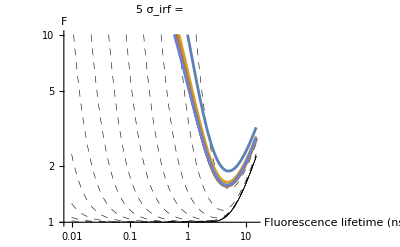

{12.5,6.25,3.125,1.5625,0.78125,0.390625,0.195313,0.0976563,0.0488281,0.0244141,0.012207,0.00610352}

```mathematica
pr=ListLogLogPlot[Table[{τ0[[τi]],√memo[[τi,mi,1]]},{mi,1,mn},{τi,1,τn}],PlotRange->{1,10},Joined->True,PlotStyle->Directive[Black,Thickness[.001],Dashed]];
For[j=1,j≤σn, j++,p0=ListLogLogPlot[Table[{τ0[[τi]],1},{mi,1,1},{τi,1,τn}],PlotRange->{1,10},Joined->True,PlotStyle->Directive[Black,Thin,SolidData]];
p1=ListLogLogPlot[Table[{τ0[[τi]],√memo[[τi,mi,j]]},{mi,1,mn},{τi,1,τn}],PlotRange->{1,10},Joined->True,PlotStyle->Directive[Thickness[.005],SolidData]];
p2=ListLogLogPlot[Table[{τ0[[τi]],√memo2[[τi,mi,j]]},{mi,1,mn},{τi,1,τn}],Joined->True,PlotStyle->Directive[Thin,Dashed]];
Print[Show[pr,p1,PlotLabel->"σ_irf = " σ0[[j]],AxesLabel->{"Fluorescence lifetime (ns)","F"}]];
Print[25./m0]

];
```

```mathematica
25./m0
```

{12.5,6.25,3.125,1.5625,0.78125,0.390625,0.195313,0.0976563,0.0488281,0.0244141,0.012207,0.00610352}

```mathematica
(* IRF has to be sampled properly. All curves with PER/m  *)
```

```mathematica
NotebookSave[]
```